# Numerical calculation of the Yukawa potential.

## Potential

For l = 0, we have:

```mathematica
V[p_,q_,m_,g_,x_] = -(4*π*g^2)/((p^2 + q^2 -2p*q*x) + m^2);
(*Integrate[1/2*V[p,q,m,g,x]*LegendreP[0,x],{x,-1,1}];*)
V0[p_,q_,m_,g_] = -(4*π*g^2 (Log[(m^2+(p+q)^2)/(m^2+(p-q)^2)]))/(4 p q);
pole1[m_,q_,z_] = p/.Solve[m^2 + (p^2 + q^2 + 2*p*q*z) == 0,p];
pole2[m_,q_,z_] = p/.Solve[m^2 + (p^2 + q^2 - 2*p*q*z) == 0,p];
```

```mathematica
V0[Sqrt[-1.0],Sqrt[-1.0],1,1]
```

3.45139+9.8696 ⅈ

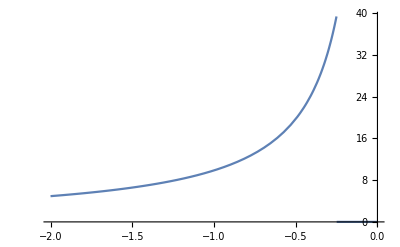

```mathematica
Show[Plot[Im[V0[Sqrt[q],Sqrt[q],1,1]],{q,-2,0},PlotRange->All]]
```

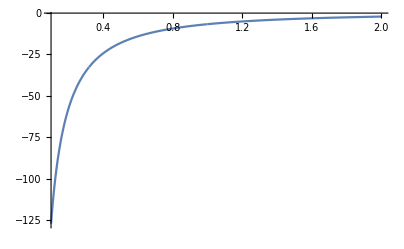

```mathematica
Show[Plot[Re[V0[p,Sqrt[-2],1,1] -(4*π*1^2 (2*π*I))/(4 (p) Sqrt[-2])],{p,0.1,1},PlotRange->All],Plot[Re[V0[p,Sqrt[-2],1,1]],{p,1,2}]]
```

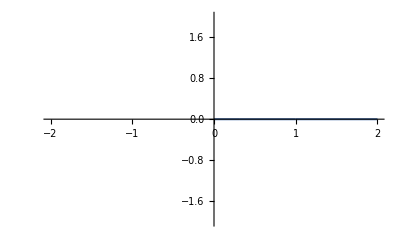

```mathematica
Show[Plot[Im[V0[p,Sqrt[-2],1,1]-(4*π*1^2 (2*π*I))/(4 (p) Sqrt[-2])],{p,0.0,1},PlotRange->{{-2,2},{-2,2}}],Plot[Im[V0[p,Sqrt[-2],1,1]],{p,1,2}]]
```

```mathematica
Sqrt[-1.4]
```

0.+1.18322 ⅈ

```mathematica
-I + Sqrt[-1.4]
```

0.+0.183216 ⅈ

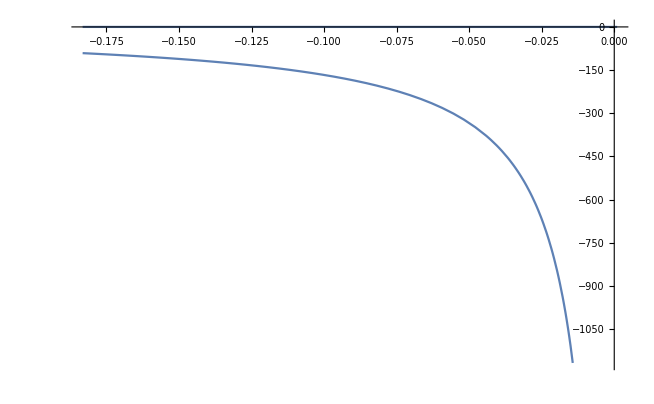

```mathematica
Show[Plot[Im[V0[I*p,Sqrt[-1.4],1,1]],{p,0.001,1-Im[Sqrt[-1.4]]},PlotRange->All],Plot[Im[V0[I*p,Sqrt[-1.4],1,1]-(4*π*1^2 (2*π*I))/(4 (I*p) Sqrt[-1.4])],{p,0.001,1-Im[Sqrt[-1.4]]}]]
```

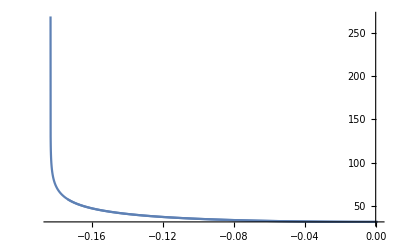

```mathematica
Show[Plot[Re[V0[I*p,Sqrt[-1.4],1,1]],{p,0.001,1-Im[Sqrt[-1.4]]},PlotRange->All],Plot[Re[V0[I*p,Sqrt[-1.4],1,1]-(4*π*1^2 (2*π*I))/(4 (I*p) Sqrt[-1.4])],{p,0.001,1-Im[Sqrt[-1.4]]}]]
```

```mathematica
pole2[m,q,z][[1]]
```

q z-√(-m^2-q^2+q^2 z^2)

```mathematica
Manipulate[Show[ParametricPlot[{ReIm[pole2[1,q,z][[1]]],ReIm[pole2[1,q,z][[2]]]},{z,-1,1},PlotStyle->{Black}],ParametricPlot[ReIm[3/4*Exp[(-3*I*π)/4]*Sqrt[-1-q^2]/2*(1- Exp[I*ϕ])],{ϕ,0,π},PlotStyle->{Orange}],ParametricPlot[ReIm[(3/4*Exp[(-3*I*π)/4]*Sqrt[-1-q^2]) + (-ⅈ √(-1-q^2)-3/4*Exp[(-3*I*π)/4]*Sqrt[-1-q^2])*z],{z,0,1.5},PlotStyle->{Orange}],ParametricPlot[ReIm[(0) + (3/4*Exp[(-3*I*π)/4]*Sqrt[-1-q^2])*z],{z,0,1.0},PlotStyle->{Orange}],ParametricPlot[ReIm[(0.795495128834866-0.7954951288348661 ⅈ) √(-1-q^2)- ((0.5303300858899107+0.4393398282201787 ⅈ) √(-1-q^2))/2*(1+Exp[I*ϕ])],{ϕ,0,π},PlotStyle->{Orange}],Graphics[{Green,PointSize[0.015],Point[ReIm[pole2[1,q,-1][[2]]]],Blue,PointSize[0.015],Point[ReIm[pole2[1,q,1][[2]]]],Red,PointSize[0.015],Point[ReIm[pole2[1,q,-1][[1]]]],Black,PointSize[0.015],Point[ReIm[pole2[1,q,1][[1]]]],Purple,Point[ReIm[V0[q,q,1,1]]],Red,PointSize[0.015],Point[ReIm[-I*pole2[1,q,0][[2]]]],Orange,PointSize[0.015],Point[ReIm[3/4(Sqrt[-1-q^2]*(-0.7071067811865475-0.7071067811865476 ⅈ))]],Orange,PointSize[0.015],Point[ReIm[(0.2651650429449552-1.2348349570550448 ⅈ) √(-1-q^2)]],Orange,PointSize[0.015],Point[ReIm[(Sqrt[-1-q^2] + 0.5)]],Orange,PointSize[0.015],Point[ReIm[(0.795495128834866-0.7954951288348661 ⅈ) √(-1-q^2)]]}],PlotRange->{{-2,2},{-2,2}}],{{q,Sqrt[-2]},Sqrt[-5],0}]
```

```mathematica
Manipulate[Show[ParametricPlot[{ReIm[pole2[1,q,z][[1]]],ReIm[pole2[1,q,z][[2]]]},{z,-1,1},PlotStyle->{Black}],ParametricPlot[ReIm[(I - q - del*I)/2(1-Exp[I*ϕ])],{ϕ,0,π},PlotStyle->Orange],ParametricPlot[ReIm[(I - q - del*I) +(-1+ 1/z)],{z,1,0},PlotStyle->Orange],ParametricPlot[ReIm[(I - q - del*I)/2*I*1/x],{x,1,0},PlotStyle->Orange],ParametricPlot[ReIm[((I - q - del*I)0.1)/2*( Exp[-I*ϕ])+ I (I - q - del*I)/2+(0.1*(I - q - del*I))/2 ],{ϕ,π,π/2},PlotStyle->Orange],Graphics[{Green,PointSize[0.015],Point[ReIm[pole2[1,q,-1][[2]]]],Blue,PointSize[0.015],Point[ReIm[pole2[1,q,1][[2]]]],Red,PointSize[0.015],Point[ReIm[pole2[1,q,-1][[1]]]],Black,PointSize[0.015],Point[ReIm[pole2[1,q,1][[1]]]],Purple,Point[ReIm[V0[q,q,1,1]]]}],PlotRange->{{-2,2},{-2,2}}],{{q,Sqrt[-2]},Sqrt[-5],0},{del,0.0,1},{μ,0.00,1}]
```

```mathematica
D[(I - q - del*I)/2(1-Exp[I*2*π*x]),x]
```

-ⅈ ⅇ^(2 ⅈ π x) π (ⅈ-ⅈ del-q)

```mathematica
((I - q - del*I)0.1)/2*( Exp[-I*ϕ])+ I (0.1*(I - q - del*I))/2+(0.1*(I - q - del*I))/2/.{ϕ->π/2}
```

```mathematica
(0.05+0. ⅈ) (ⅈ-ⅈ del-q)
```

(0.05+0. ⅈ) (ⅈ-ⅈ del-q)

```mathematica
(0.05+0.45 ⅈ) (ⅈ-ⅈ del-q)/.{del->0,q->Sqrt[-2]}
```

0.186396-0.0207107 ⅈ

```mathematica
(0.05+0.45 ⅈ) (ⅈ-ⅈ del-q)/.{del->0,q->Sqrt[-2]}
```

0.186396-0.0207107 ⅈ

```mathematica
(0.05+0.45 ⅈ) (ⅈ-ⅈ del-q)/.{del->0,q->Sqrt[-2]}
```

0.186396-0.0207107 ⅈ

```mathematica
FullSimplify[(1/2+ⅈ/2) (ⅈ-ⅈ del-q)//N]
```

```mathematica
(-0.5+0.5 ⅈ)+(0.5-0.5 ⅈ) del-(0.5+0.5 ⅈ) q/.{del->0,q->Sqrt[-2]}
```

0.207107-0.207107 ⅈ

```mathematica
(I - q - del*I)/2(1-Exp[I*3 π/2])
```

```mathematica
(1/2+ⅈ/2) (ⅈ-ⅈ del-q)/.{del->0,q->Sqrt[-2]}
```

```mathematica
(1/2+ⅈ/2) (ⅈ-ⅈ √2)//N
```

0.207107-0.207107 ⅈ

```mathematica
Exp[I*π/2]
```

ⅈ

```mathematica
(I - q - del*I)/2(1-Exp[I*3*π/2])
```

```mathematica
(1/2+ⅈ/2) (ⅈ-ⅈ del-q)//FullSimplify
```

(1/2-ⅈ/2) (-1+del-ⅈ q)

```mathematica
(I - q - del*I)/2 0.1 *( Exp[-I*π/2])+ I (I - q - del*I)/2+(0.1*(I - q - del*I))/2
```

(0.05+0.45 ⅈ) (ⅈ-ⅈ del-q)

```mathematica
P1[q_] = Array[ (3/4*Exp[(-3*I*π)/4]*Sqrt[-1-q^2])*#&,100,{0,1}]//N;
```

```mathematica
P2[q_] = Array[(3/4*Exp[(-3*I*π)/4]*Sqrt[-1-q^2]) + (-ⅈ √(-1-q^2)-3/4*Exp[(-3*I*π)/4]*Sqrt[-1-q^2])*#&,100,{0,1.5}]//N;
```

```mathematica
Q[q_] = Join[P1[q],P2[q]];
```

```mathematica
A1 = Table[V0[Q[Sqrt[-2]][[i]],Sqrt[-2],1,1],{i,2,200}];
```

```mathematica
Re[A1];
```

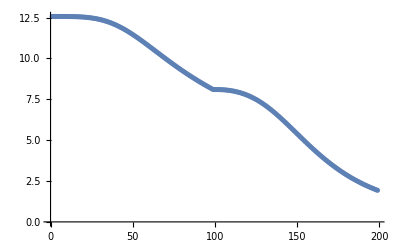

```mathematica
ListPlot[%14]
```

```mathematica
Im[A1];
```

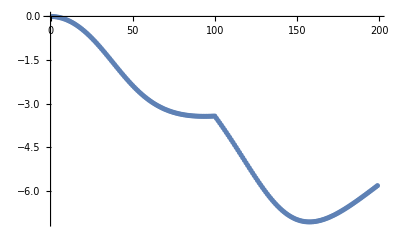

```mathematica
ListPlot[%19]
```

```mathematica
P1[q_] = Array[ (3/4*Exp[(-3*I*π)/4]*Sqrt[-1-q^2]/2*(1- Exp[I*π*#]))&,100,{0,1}]//N;
P2[q_] = Array[(3/4*Exp[(-3*I*π)/4]*Sqrt[-1-q^2]) + (-ⅈ √(-1-q^2)-3/4*Exp[(-3*I*π)/4]*Sqrt[-1-q^2])*#&,100,{0,1.5}]//N;
Q[q_] = Join[P1[q],P2[q]];
```

```mathematica
A1 = Table[V0[Q[Sqrt[-2]][[i]],Sqrt[-2],1,1],{i,2,200}];
```

```mathematica
Re[A1];
```

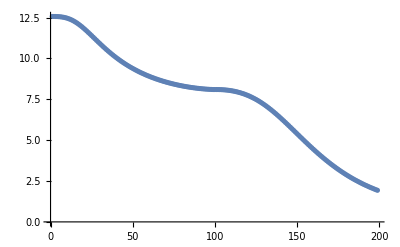

```mathematica
ListPlot[%28]
```

```mathematica
Im[A1];
```

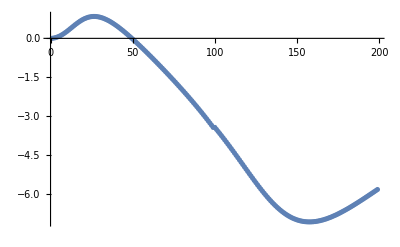

```mathematica
ListPlot[%31]
```

```mathematica
(6.2936163062465855*^-6+0.4992067018082596 ⅈ) ((0.+1. ⅈ)-1. q)/.{q->Sqrt[-2]}
```

0.206778-2.6069×10^-6 ⅈ

```mathematica
(0.+0.5 ⅈ) ((0.+1. ⅈ)-1. q)/.{q->Sqrt[-2]}
```

{0.,(-0.00535687-0.00535687 ⅈ) √(-1.-1. q^2),(-0.0107137-0.0107137 ⅈ) √(-1.-1. q^2),(-0.0160706-0.0160706 ⅈ) √(-1.-1. q^2),(-0.0214275-0.0214275 ⅈ) √(-1.-1. q^2),(-0.0267843-0.0267843 ⅈ) √(-1.-1. q^2),(-0.0321412-0.0321412 ⅈ) √(-1.-1. q^2),(-0.0374981-0.0374981 ⅈ) √(-1.-1. q^2),(-0.042855-0.042855 ⅈ) √(-1.-1. q^2),(-0.0482118-0.0482118 ⅈ) √(-1.-1. q^2),(-0.0535687-0.0535687 ⅈ) √(-1.-1. q^2),(-0.0589256-0.0589256 ⅈ) √(-1.-1. q^2),(-0.0642824-0.0642824 ⅈ) √(-1.-1. q^2),(-0.0696393-0.0696393 ⅈ) √(-1.-1. q^2),(-0.0749962-0.0749962 ⅈ) √(-1.-1. q^2),(-0.080353-0.080353 ⅈ) √(-1.-1. q^2),(-0.0857099-0.0857099 ⅈ) √(-1.-1. q^2),(-0.0910668-0.0910668 ⅈ) √(-1.-1. q^2),(-0.0964237-0.0964237 ⅈ) √(-1.-1. q^2),(-0.101781-0.101781 ⅈ) √(-1.-1. q^2),(-0.107137-0.107137 ⅈ) √(-1.-1. q^2),(-0.112494-0.112494 ⅈ) √(-1.-1. q^2),(-0.117851-0.117851 ⅈ) √(-1.-1. q^2),(-0.123208-0.123208 ⅈ) √(-1.-1. q^2),(-0.128565-0.128565 ⅈ) √(-1.-1. q^2),(-0.133922-0.133922 ⅈ) √(-1.-1. q^2),(-0.139279-0.139279 ⅈ) √(-1.-1. q^2),(-0.144635-0.144635 ⅈ) √(-1.-1. q^2),(-0.149992-0.149992 ⅈ) √(-1.-1. q^2),(-0.155349-0.155349 ⅈ) √(-1.-1. q^2),(-0.160706-0.160706 ⅈ) √(-1.-1. q^2),(-0.166063-0.166063 ⅈ) √(-1.-1. q^2),(-0.17142-0.17142 ⅈ) √(-1.-1. q^2),(-0.176777-0.176777 ⅈ) √(-1.-1. q^2),(-0.182134-0.182134 ⅈ) √(-1.-1. q^2),(-0.18749-0.18749 ⅈ) √(-1.-1. q^2),(-0.192847-0.192847 ⅈ) √(-1.-1. q^2),(-0.198204-0.198204 ⅈ) √(-1.-1. q^2),(-0.203561-0.203561 ⅈ) √(-1.-1. q^2),(-0.208918-0.208918 ⅈ) √(-1.-1. q^2),(-0.214275-0.214275 ⅈ) √(-1.-1. q^2),(-0.219632-0.219632 ⅈ) √(-1.-1. q^2),(-0.224989-0.224989 ⅈ) √(-1.-1. q^2),(-0.230345-0.230345 ⅈ) √(-1.-1. q^2),(-0.235702-0.235702 ⅈ) √(-1.-1. q^2),(-0.241059-0.241059 ⅈ) √(-1.-1. q^2),(-0.246416-0.246416 ⅈ) √(-1.-1. q^2),(-0.251773-0.251773 ⅈ) √(-1.-1. q^2),(-0.25713-0.25713 ⅈ) √(-1.-1. q^2),(-0.262487-0.262487 ⅈ) √(-1.-1. q^2),(-0.267843-0.267843 ⅈ) √(-1.-1. q^2),(-0.2732-0.2732 ⅈ) √(-1.-1. q^2),(-0.278557-0.278557 ⅈ) √(-1.-1. q^2),(-0.283914-0.283914 ⅈ) √(-1.-1. q^2),(-0.289271-0.289271 ⅈ) √(-1.-1. q^2),(-0.294628-0.294628 ⅈ) √(-1.-1. q^2),(-0.299985-0.299985 ⅈ) √(-1.-1. q^2),(-0.305342-0.305342 ⅈ) √(-1.-1. q^2),(-0.310698-0.310698 ⅈ) √(-1.-1. q^2),(-0.316055-0.316055 ⅈ) √(-1.-1. q^2),(-0.321412-0.321412 ⅈ) √(-1.-1. q^2),(-0.326769-0.326769 ⅈ) √(-1.-1. q^2),(-0.332126-0.332126 ⅈ) √(-1.-1. q^2),(-0.337483-0.337483 ⅈ) √(-1.-1. q^2),(-0.34284-0.34284 ⅈ) √(-1.-1. q^2),(-0.348197-0.348197 ⅈ) √(-1.-1. q^2),(-0.353553-0.353553 ⅈ) √(-1.-1. q^2),(-0.35891-0.35891 ⅈ) √(-1.-1. q^2),(-0.364267-0.364267 ⅈ) √(-1.-1. q^2),(-0.369624-0.369624 ⅈ) √(-1.-1. q^2),(-0.374981-0.374981 ⅈ) √(-1.-1. q^2),(-0.380338-0.380338 ⅈ) √(-1.-1. q^2),(-0.385695-0.385695 ⅈ) √(-1.-1. q^2),(-0.391051-0.391051 ⅈ) √(-1.-1. q^2),(-0.396408-0.396408 ⅈ) √(-1.-1. q^2),(-0.401765-0.401765 ⅈ) √(-1.-1. q^2),(-0.407122-0.407122 ⅈ) √(-1.-1. q^2),(-0.412479-0.412479 ⅈ) √(-1.-1. q^2),(-0.417836-0.417836 ⅈ) √(-1.-1. q^2),(-0.423193-0.423193 ⅈ) √(-1.-1. q^2),(-0.42855-0.42855 ⅈ) √(-1.-1. q^2),(-0.433906-0.433906 ⅈ) √(-1.-1. q^2),(-0.439263-0.439263 ⅈ) √(-1.-1. q^2),(-0.44462-0.44462 ⅈ) √(-1.-1. q^2),(-0.449977-0.449977 ⅈ) √(-1.-1. q^2),(-0.455334-0.455334 ⅈ) √(-1.-1. q^2),(-0.460691-0.460691 ⅈ) √(-1.-1. q^2),(-0.466048-0.466048 ⅈ) √(-1.-1. q^2),(-0.471405-0.471405 ⅈ) √(-1.-1. q^2),(-0.476761-0.476761 ⅈ) √(-1.-1. q^2),(-0.482118-0.482118 ⅈ) √(-1.-1. q^2),(-0.487475-0.487475 ⅈ) √(-1.-1. q^2),(-0.492832-0.492832 ⅈ) √(-1.-1. q^2),(-0.498189-0.498189 ⅈ) √(-1.-1. q^2),(-0.503546-0.503546 ⅈ) √(-1.-1. q^2),(-0.508903-0.508903 ⅈ) √(-1.-1. q^2),(-0.514259-0.514259 ⅈ) √(-1.-1. q^2),(-0.519616-0.519616 ⅈ) √(-1.-1. q^2),(-0.524973-0.524973 ⅈ) √(-1.-1. q^2),(-0.53033-0.53033 ⅈ) √(-1.-1. q^2)}

```mathematica
Q1[q_] = Array[(-1+ 1/#)&,100,{1,0}]//N
```

Power::infy: Infinite expression 1/0 encountered.

{0.,0.0102041,0.0206186,0.03125,0.0421053,0.0531915,0.0645161,0.076087,0.0879121,0.1,0.11236,0.125,0.137931,0.151163,0.164706,0.178571,0.192771,0.207317,0.222222,0.2375,0.253165,0.269231,0.285714,0.302632,0.32,0.337838,0.356164,0.375,0.394366,0.414286,0.434783,0.455882,0.477612,0.5,0.523077,0.546875,0.571429,0.596774,0.622951,0.65,0.677966,0.706897,0.736842,0.767857,0.8,0.833333,0.867925,0.903846,0.941176,0.98,1.02041,1.0625,1.10638,1.15217,1.2,1.25,1.30233,1.35714,1.41463,1.475,1.53846,1.60526,1.67568,1.75,1.82857,1.91176,2.,2.09375,2.19355,2.3,2.41379,2.53571,2.66667,2.80769,2.96,3.125,3.30435,3.5,3.71429,3.95,4.21053,4.5,4.82353,5.1875,5.6,6.07143,6.61538,7.25,8.,8.9,10.,11.375,13.1429,15.5,18.8,23.75,32.,48.5,98.,ComplexInfinity}

```mathematica
Q[q_]=Join[P1[q],Q1[q]]
```

{0.,(0.000251729-0.015864 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.00100666-0.031712 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.00226404-0.047528 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.00402259-0.0632962 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.00628056-0.0790007 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.00903565-0.0946256 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0122851-0.110155 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0160256-0.125574 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0202535-0.140866 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0249644-0.156017 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0301537-0.17101 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.035816-0.185831 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0419458-0.200465 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0485367-0.214897 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0555823-0.229113 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0630753-0.243098 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0710083-0.256839 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0793732-0.27032 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0881617-0.28353 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.0973649-0.296454 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.106973-0.309079 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.116978-0.321394 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.127368-0.333385 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.138133-0.34504 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.149263-0.356347 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.160745-0.367296 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.17257-0.377875 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.184724-0.388073 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.197195-0.397881 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.209972-0.407288 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.22304-0.416285 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.236387-0.424863 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.25-0.433013 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.263864-0.440727 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.277967-0.447997 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.292292-0.454816 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.306827-0.461177 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.321557-0.467074 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.336466-0.4725 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.35154-0.477451 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.366763-0.481921 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.382121-0.485906 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.397597-0.489401 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.413176-0.492404 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.428843-0.494911 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.444581-0.496919 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.460375-0.498427 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.476209-0.499434 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.492067-0.499937 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.507933-0.499937 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.523791-0.499434 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.539625-0.498427 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.555419-0.496919 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.571157-0.494911 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.586824-0.492404 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.602403-0.489401 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.617879-0.485906 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.633237-0.481921 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.64846-0.477451 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.663534-0.4725 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.678443-0.467074 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.693173-0.461177 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.707708-0.454816 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.722033-0.447997 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.736136-0.440727 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.75-0.433013 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.763613-0.424863 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.77696-0.416285 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.790028-0.407288 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.802805-0.397881 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.815276-0.388073 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.82743-0.377875 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.839255-0.367296 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.850737-0.356347 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.861867-0.34504 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.872632-0.333385 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.883022-0.321394 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.893027-0.309079 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.902635-0.296454 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.911838-0.28353 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.920627-0.27032 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.928992-0.256839 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.936925-0.243098 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.944418-0.229113 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.951463-0.214897 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.958054-0.200465 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.964184-0.185831 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.969846-0.17101 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.975036-0.156017 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.979746-0.140866 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.983974-0.125574 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.987715-0.110155 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.990964-0.0946256 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.993719-0.0790007 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.995977-0.0632962 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.997736-0.047528 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.998993-0.031712 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.999748-0.015864 ⅈ) ((0.+0.9 ⅈ)-1. q),(0.+0.9 ⅈ)-1. q,(0.+0.9 ⅈ)-1. q,(0.0102041+0.9 ⅈ)-1. q,(0.0206186+0.9 ⅈ)-1. q,(0.03125+0.9 ⅈ)-1. q,(0.0421053+0.9 ⅈ)-1. q,(0.0531915+0.9 ⅈ)-1. q,(0.0645161+0.9 ⅈ)-1. q,(0.076087+0.9 ⅈ)-1. q,(0.0879121+0.9 ⅈ)-1. q,(0.1+0.9 ⅈ)-1. q,(0.11236+0.9 ⅈ)-1. q,(0.125+0.9 ⅈ)-1. q,(0.137931+0.9 ⅈ)-1. q,(0.151163+0.9 ⅈ)-1. q,(0.164706+0.9 ⅈ)-1. q,(0.178571+0.9 ⅈ)-1. q,(0.192771+0.9 ⅈ)-1. q,(0.207317+0.9 ⅈ)-1. q,(0.222222+0.9 ⅈ)-1. q,(0.2375+0.9 ⅈ)-1. q,(0.253165+0.9 ⅈ)-1. q,(0.269231+0.9 ⅈ)-1. q,(0.285714+0.9 ⅈ)-1. q,(0.302632+0.9 ⅈ)-1. q,(0.32+0.9 ⅈ)-1. q,(0.337838+0.9 ⅈ)-1. q,(0.356164+0.9 ⅈ)-1. q,(0.375+0.9 ⅈ)-1. q,(0.394366+0.9 ⅈ)-1. q,(0.414286+0.9 ⅈ)-1. q,(0.434783+0.9 ⅈ)-1. q,(0.455882+0.9 ⅈ)-1. q,(0.477612+0.9 ⅈ)-1. q,(0.5+0.9 ⅈ)-1. q,(0.523077+0.9 ⅈ)-1. q,(0.546875+0.9 ⅈ)-1. q,(0.571429+0.9 ⅈ)-1. q,(0.596774+0.9 ⅈ)-1. q,(0.622951+0.9 ⅈ)-1. q,(0.65+0.9 ⅈ)-1. q,(0.677966+0.9 ⅈ)-1. q,(0.706897+0.9 ⅈ)-1. q,(0.736842+0.9 ⅈ)-1. q,(0.767857+0.9 ⅈ)-1. q,(0.8+0.9 ⅈ)-1. q,(0.833333+0.9 ⅈ)-1. q,(0.867925+0.9 ⅈ)-1. q,(0.903846+0.9 ⅈ)-1. q,(0.941176+0.9 ⅈ)-1. q,(0.98+0.9 ⅈ)-1. q,(1.02041+0.9 ⅈ)-1. q,(1.0625+0.9 ⅈ)-1. q,(1.10638+0.9 ⅈ)-1. q,(1.15217+0.9 ⅈ)-1. q,(1.2+0.9 ⅈ)-1. q,(1.25+0.9 ⅈ)-1. q,(1.30233+0.9 ⅈ)-1. q,(1.35714+0.9 ⅈ)-1. q,(1.41463+0.9 ⅈ)-1. q,(1.475+0.9 ⅈ)-1. q,(1.53846+0.9 ⅈ)-1. q,(1.60526+0.9 ⅈ)-1. q,(1.67568+0.9 ⅈ)-1. q,(1.75+0.9 ⅈ)-1. q,(1.82857+0.9 ⅈ)-1. q,(1.91176+0.9 ⅈ)-1. q,(2.+0.9 ⅈ)-1. q,(2.09375+0.9 ⅈ)-1. q,(2.19355+0.9 ⅈ)-1. q,(2.3+0.9 ⅈ)-1. q,(2.41379+0.9 ⅈ)-1. q,(2.53571+0.9 ⅈ)-1. q,(2.66667+0.9 ⅈ)-1. q,(2.80769+0.9 ⅈ)-1. q,(2.96+0.9 ⅈ)-1. q,(3.125+0.9 ⅈ)-1. q,(3.30435+0.9 ⅈ)-1. q,(3.5+0.9 ⅈ)-1. q,(3.71429+0.9 ⅈ)-1. q,(3.95+0.9 ⅈ)-1. q,(4.21053+0.9 ⅈ)-1. q,(4.5+0.9 ⅈ)-1. q,(4.82353+0.9 ⅈ)-1. q,(5.1875+0.9 ⅈ)-1. q,(5.6+0.9 ⅈ)-1. q,(6.07143+0.9 ⅈ)-1. q,(6.61538+0.9 ⅈ)-1. q,(7.25+0.9 ⅈ)-1. q,(8.+0.9 ⅈ)-1. q,(8.9+0.9 ⅈ)-1. q,(10.+0.9 ⅈ)-1. q,(11.375+0.9 ⅈ)-1. q,(13.1429+0.9 ⅈ)-1. q,(15.5+0.9 ⅈ)-1. q,(18.8+0.9 ⅈ)-1. q,(23.75+0.9 ⅈ)-1. q,(32.+0.9 ⅈ)-1. q,(48.5+0.9 ⅈ)-1. q,(98.+0.9 ⅈ)-1. q,ComplexInfinity}

```mathematica
A1 = Table[V0[Q[Sqrt[-2]][[i]],Sqrt[-2],1,1],{i,2,199}]
```

{12.565-0.0000442099 ⅈ,12.5608-0.000352923 ⅈ,12.5539-0.00118689 ⅈ,12.5444-0.00279949 ⅈ,12.5322-0.00543338 ⅈ,12.5176-0.00931745 ⅈ,12.5007-0.0146643 ⅈ,12.4816-0.0216683 ⅈ,12.4605-0.0305038 ⅈ,12.4375-0.0413246 ⅈ,12.4129-0.054263 ⅈ,12.3869-0.0694306 ⅈ,12.3595-0.086918 ⅈ,12.3311-0.106796 ⅈ,12.3018-0.129118 ⅈ,12.2717-0.153919 ⅈ,12.2411-0.181219 ⅈ,12.2102-0.211025 ⅈ,12.179-0.243329 ⅈ,12.1478-0.278117 ⅈ,12.1166-0.315364 ⅈ,12.0857-0.355037 ⅈ,12.0551-0.397099 ⅈ,12.0249-0.441508 ⅈ,11.9953-0.48822 ⅈ,11.9663-0.537188 ⅈ,11.9381-0.588365 ⅈ,11.9106-0.641705 ⅈ,11.884-0.69716 ⅈ,11.8584-0.754687 ⅈ,11.8337-0.814243 ⅈ,11.81-0.875787 ⅈ,11.7874-0.939284 ⅈ,11.766-1.0047 ⅈ,11.7456-1.07201 ⅈ,11.7265-1.14117 ⅈ,11.7085-1.21219 ⅈ,11.6918-1.28502 ⅈ,11.6763-1.35967 ⅈ,11.6621-1.43612 ⅈ,11.6492-1.51438 ⅈ,11.6376-1.59443 ⅈ,11.6273-1.6763 ⅈ,11.6183-1.75998 ⅈ,11.6106-1.84551 ⅈ,11.6043-1.93289 ⅈ,11.5994-2.02216 ⅈ,11.5958-2.11336 ⅈ,11.5936-2.20651 ⅈ,11.5929-2.30167 ⅈ,11.5935-2.39889 ⅈ,11.5955-2.49823 ⅈ,11.5989-2.59976 ⅈ,11.6038-2.70354 ⅈ,11.6102-2.80966 ⅈ,11.6179-2.91821 ⅈ,11.6272-3.02928 ⅈ,11.6379-3.14298 ⅈ,11.6502-3.25944 ⅈ,11.6639-3.37878 ⅈ,11.6791-3.50113 ⅈ,11.6958-3.62666 ⅈ,11.7141-3.75552 ⅈ,11.7339-3.88789 ⅈ,11.7551-4.02398 ⅈ,11.778-4.16398 ⅈ,11.8023-4.30814 ⅈ,11.8281-4.4567 ⅈ,11.8553-4.60993 ⅈ,11.884-4.76812 ⅈ,11.9141-4.93161 ⅈ,11.9454-5.10072 ⅈ,11.9781-5.27584 ⅈ,12.0118-5.45737 ⅈ,12.0466-5.64574 ⅈ,12.0822-5.84145 ⅈ,12.1185-6.04498 ⅈ,12.1552-6.25689 ⅈ,12.192-6.47777 ⅈ,12.2285-6.70824 ⅈ,12.2644-6.94895 ⅈ,12.299-7.20061 ⅈ,12.3317-7.46391 ⅈ,12.3618-7.7396 ⅈ,12.3884-8.0284 ⅈ,12.4104-8.33103 ⅈ,12.4265-8.64815 ⅈ,12.4354-8.98035 ⅈ,12.4354-9.32811 ⅈ,12.4247-9.6917 ⅈ,12.4013-10.0712 ⅈ,12.363-10.4664 ⅈ,12.3076-10.8768 ⅈ,12.2327-11.3012 ⅈ,12.1361-11.7385 ⅈ,12.0157-12.1866 ⅈ,11.8697-12.6434 ⅈ,11.6966-13.1061 ⅈ,11.4954-13.5719 ⅈ,11.4954-13.5719 ⅈ,11.731+12.9856 ⅈ,11.9032+12.3894 ⅈ,12.0131+11.7959 ⅈ,12.0651+11.216 ⅈ,12.0659+10.6585 ⅈ,12.0236+10.1296 ⅈ,11.9466+9.63271 ⅈ,11.8428+9.16901 ⅈ,11.719+8.73808 ⅈ,11.5809+8.33842 ⅈ,11.4332+7.96786 ⅈ,11.2794+7.62398 ⅈ,11.1222+7.30426 ⅈ,10.9637+7.00629 ⅈ,10.8052+6.72779 ⅈ,10.6479+6.46672 ⅈ,10.4925+6.2212 ⅈ,10.3393+5.98959 ⅈ,10.1888+5.77043 ⅈ,10.041+5.56243 ⅈ,9.89604+5.36447 ⅈ,9.75384+5.17555 ⅈ,9.61433+4.99482 ⅈ,9.47742+4.82149 ⅈ,9.34298+4.65493 ⅈ,9.21084+4.49453 ⅈ,9.08086+4.33979 ⅈ,8.95286+4.19026 ⅈ,8.82669+4.04554 ⅈ,8.70217+3.9053 ⅈ,8.57914+3.76923 ⅈ,8.45745+3.63707 ⅈ,8.33695+3.50859 ⅈ,8.21749+3.38358 ⅈ,8.09892+3.26188 ⅈ,7.98113+3.14333 ⅈ,7.86399+3.02781 ⅈ,7.74737+2.91519 ⅈ,7.63118+2.80539 ⅈ,7.51531+2.69833 ⅈ,7.39967+2.59392 ⅈ,7.28417+2.49212 ⅈ,7.16873+2.39288 ⅈ,7.05329+2.29614 ⅈ,6.93778+2.20188 ⅈ,-5.08133-4.94229 ⅈ,-4.96022-4.6166 ⅈ,-4.83067-4.30615 ⅈ,-4.69392-4.01077 ⅈ,-4.55111-3.73023 ⅈ,-4.40332-3.46424 ⅈ,-4.25155-3.21244 ⅈ,-4.09673-2.97445 ⅈ,-3.93971-2.74985 ⅈ,-3.78129-2.53819 ⅈ,-3.62219-2.33902 ⅈ,-3.46307-2.15186 ⅈ,-3.30452-1.97622 ⅈ,-3.14709-1.81163 ⅈ,-2.99126-1.65758 ⅈ,-2.83748-1.51362 ⅈ,-2.68612-1.37926 ⅈ,-2.53756-1.25404 ⅈ,-2.39209-1.13752 ⅈ,-2.24998-1.02926 ⅈ,-2.11149-0.92883 ⅈ,-1.97682-0.835829 ⅈ,-1.84615-0.749865 ⅈ,-1.71964-0.670561 ⅈ,-1.59743-0.597556 ⅈ,-1.47963-0.530503 ⅈ,-1.36634-0.469072 ⅈ,-1.25764-0.412943 ⅈ,-1.15358-0.361813 ⅈ,-1.05422-0.315388 ⅈ,-0.959586-0.273387 ⅈ,-0.869706-0.235538 ⅈ,-0.784587-0.201581 ⅈ,-0.704225-0.171261 ⅈ,-0.628608-0.144335 ⅈ,-0.557711-0.120563 ⅈ,-0.491498-0.0997144 ⅈ,-0.429923-0.0815647 ⅈ,-0.372929-0.0658946 ⅈ,-0.320449-0.0524912 ⅈ,-0.272406-0.0411473 ⅈ,-0.228711-0.0316621 ⅈ,-0.189267-0.0238414 ⅈ,-0.153968-0.0174978 ⅈ,-0.122698-0.0124512 ⅈ,-0.0953319-0.0085296 ⅈ,-0.0717384-0.00556941 ⅈ,-0.0517792-0.00341597 ⅈ,-0.03531-0.00192404 ⅈ,-0.0221819-0.000958161 ⅈ,-0.0122425-0.000392918 ⅈ,-0.0053367-0.000113096 ⅈ,-0.00130812-0.0000137256 ⅈ}

```mathematica
A1 = Table[V0[P1[Sqrt[-2]][[i]],Sqrt[-2],1,1],{i,2,50}]
```

{12.5584-0.000503141 ⅈ,12.535-0.0039818 ⅈ,12.497-0.0132029 ⅈ,12.4461-0.0305506 ⅈ,12.384-0.0579124 ⅈ,12.313-0.0966327 ⅈ,12.235-0.147529 ⅈ,12.1523-0.210956 ⅈ,12.0665-0.286892 ⅈ,11.9793-0.375038 ⅈ,11.892-0.474907 ⅈ,11.8057-0.585907 ⅈ,11.7212-0.707401 ⅈ,11.6391-0.838756 ⅈ,11.5598-0.979379 ⅈ,11.4836-1.12873 ⅈ,11.4107-1.28636 ⅈ,11.341-1.45187 ⅈ,11.2745-1.62496 ⅈ,11.211-1.80543 ⅈ,11.1505-1.99312 ⅈ,11.0927-2.18798 ⅈ,11.0373-2.39002 ⅈ,10.9839-2.59931 ⅈ,10.9324-2.81601 ⅈ,10.8821-3.04033 ⅈ,10.8328-3.27254 ⅈ,10.7839-3.51295 ⅈ,10.7349-3.76196 ⅈ,10.6851-4.01998 ⅈ,10.6339-4.2875 ⅈ,10.5805-4.56502 ⅈ,10.524-4.85307 ⅈ,10.4635-5.15221 ⅈ,10.3979-5.46301 ⅈ,10.3258-5.78601 ⅈ,10.2459-6.12172 ⅈ,10.1567-6.47058 ⅈ,10.0564-6.83295 ⅈ,9.9431-7.20904 ⅈ,9.81481-7.59888 ⅈ,9.66932-8.0023 ⅈ,9.50436-8.41883 ⅈ,9.31759-8.84772 ⅈ,9.10669-9.28788 ⅈ,8.86941-9.73787 ⅈ,8.60371-10.1959 ⅈ,8.30774-10.66 ⅈ,7.98003-11.1278 ⅈ}

```mathematica
A3 = Table[V0[P1[Sqrt[-2]][[i]],Sqrt[-2],1,1]-(4*π*1^2 (2*π*I))/(4 (P1[Sqrt[-2]][[i]]) Sqrt[-2]),{i,51,99}]
```

{7.61944-11.5968 ⅈ,7.22524-12.0646 ⅈ,6.7971-12.5286 ⅈ,6.33505-12.9867 ⅈ,5.83939-13.4367 ⅈ,5.31064-13.8768 ⅈ,4.74943-14.3057 ⅈ,4.15641-14.7223 ⅈ,3.53214-15.1257 ⅈ,2.87705-15.5155 ⅈ,2.19133-15.8916 ⅈ,1.47489-16.254 ⅈ,0.727317-16.6028 ⅈ,-0.0521672-16.9385 ⅈ,-0.864732-17.2615 ⅈ,-1.71198-17.5723 ⅈ,-2.59598-17.8715 ⅈ,-3.51929-18.1595 ⅈ,-4.48505-18.4371 ⅈ,-5.49697-18.7046 ⅈ,-6.55951-18.9626 ⅈ,-7.67785-19.2116 ⅈ,-8.85813-19.452 ⅈ,-10.1075-19.6842 ⅈ,-11.4345-19.9085 ⅈ,-12.8489-20.1252 ⅈ,-14.3625-20.3345 ⅈ,-15.9894-20.5366 ⅈ,-17.7461-20.7314 ⅈ,-19.6528-20.9191 ⅈ,-21.7338-21.0996 ⅈ,-24.0191-21.2727 ⅈ,-26.5456-21.4382 ⅈ,-29.3596-21.5958 ⅈ,-32.5196-21.7452 ⅈ,-36.1013-21.8858 ⅈ,-40.2034-22.0172 ⅈ,-44.9575-22.1386 ⅈ,-50.5432-22.2496 ⅈ,-57.2118-22.3495 ⅈ,-65.3262-22.4377 ⅈ,-75.4304-22.5136 ⅈ,-88.3784-22.577 ⅈ,-105.593-22.6279 ⅈ,-129.634-22.6666 ⅈ,-165.619-22.694 ⅈ,-225.485-22.7113 ⅈ,-345.04-22.7206 ⅈ,-703.313-22.724 ⅈ}

```mathematica
A2 =Table[V0[Q1[Sqrt[-2]][[i]],Sqrt[-2],1,1] -(4*π*1^2 (2*π*I))/(4 (Q1[Sqrt[-2]][[i]]) Sqrt[-2]) ,{i,2,99}]
```

{-1355.29+0. ⅈ,-664.392+0. ⅈ,-434.101+0. ⅈ,-318.967+0. ⅈ,-249.898+0. ⅈ,-203.864+0. ⅈ,-170.997+0. ⅈ,-146.36+0. ⅈ,-127.213+0. ⅈ,-111.911+0. ⅈ,-99.406+0. ⅈ,-89.0012+0. ⅈ,-80.2132+0. ⅈ,-72.6969+0. ⅈ,-66.1993+0. ⅈ,-60.5303+0. ⅈ,-55.5449+0. ⅈ,-51.1298+0. ⅈ,-47.1959+0. ⅈ,-43.6717+0. ⅈ,-40.4991+0. ⅈ,-37.6306+0. ⅈ,-35.0271+0. ⅈ,-32.6557+0. ⅈ,-30.4887+0. ⅈ,-28.5028+0. ⅈ,-26.6779+0. ⅈ,-24.9969+0. ⅈ,-23.4448+0. ⅈ,-22.0088+0. ⅈ,-20.6775+0. ⅈ,-19.441+0. ⅈ,-18.2906+0. ⅈ,-17.2185+0. ⅈ,-16.2179+0. ⅈ,-15.2827+0. ⅈ,-14.4073+0. ⅈ,-13.5869+0. ⅈ,-12.8171+0. ⅈ,-12.0938+0. ⅈ,-11.4136+0. ⅈ,-10.7731+0. ⅈ,-10.1694+0. ⅈ,-9.59981+0. ⅈ,-9.06195+0. ⅈ,-8.55359+0. ⅈ,-8.07269+0. ⅈ,-7.6174+0. ⅈ,-7.18605+0. ⅈ,-20.4557+0. ⅈ,-19.5258+0. ⅈ,-18.6364+0. ⅈ,-17.7852-4.28112×10^-16 ⅈ,-16.9699+0. ⅈ,-16.1885+0. ⅈ,-15.4392+0. ⅈ,-14.7202+0. ⅈ,-14.03+0. ⅈ,-13.367+0. ⅈ,-12.7298+0. ⅈ,-12.1173+0. ⅈ,-11.5282+0. ⅈ,-10.9614+0. ⅈ,-10.4159+0. ⅈ,-9.89078+0. ⅈ,-9.38509+0. ⅈ,-8.89801+0. ⅈ,-8.42879+0. ⅈ,-7.97671+0. ⅈ,-7.54108+0. ⅈ,-7.12128+0. ⅈ,-6.71671+0. ⅈ,-6.32682+0. ⅈ,-5.95108+0. ⅈ,-5.589+0. ⅈ,-5.24011+1.49276×10^-16 ⅈ,-4.90396+0. ⅈ,-4.58012+0. ⅈ,-4.26819+0. ⅈ,-3.96777+0. ⅈ,-3.6785+0. ⅈ,-3.40001+0. ⅈ,-3.13194+0. ⅈ,-2.87396+0. ⅈ,-2.62572+0. ⅈ,-2.38689+0. ⅈ,-2.15716+0. ⅈ,-1.93621+0. ⅈ,-1.72373+0. ⅈ,-1.51941+0. ⅈ,-1.32295+0. ⅈ,-1.13406+0. ⅈ,-0.952446+0. ⅈ,-0.777821+0. ⅈ,-0.609907+0. ⅈ,-0.448431+0. ⅈ,-0.293127+0. ⅈ,-0.143734+0. ⅈ}

```mathematica
Re[Join[A1,A3,A2]]
```

{12.5584,12.535,12.497,12.4461,12.384,12.313,12.235,12.1523,12.0665,11.9793,11.892,11.8057,11.7212,11.6391,11.5598,11.4836,11.4107,11.341,11.2745,11.211,11.1505,11.0927,11.0373,10.9839,10.9324,10.8821,10.8328,10.7839,10.7349,10.6851,10.6339,10.5805,10.524,10.4635,10.3979,10.3258,10.2459,10.1567,10.0564,9.9431,9.81481,9.66932,9.50436,9.31759,9.10669,8.86941,8.60371,8.30774,7.98003,7.61944,7.22524,6.7971,6.33505,5.83939,5.31064,4.74943,4.15641,3.53214,2.87705,2.19133,1.47489,0.727317,-0.0521672,-0.864732,-1.71198,-2.59598,-3.51929,-4.48505,-5.49697,-6.55951,-7.67785,-8.85813,-10.1075,-11.4345,-12.8489,-14.3625,-15.9894,-17.7461,-19.6528,-21.7338,-24.0191,-26.5456,-29.3596,-32.5196,-36.1013,-40.2034,-44.9575,-50.5432,-57.2118,-65.3262,-75.4304,-88.3784,-105.593,-129.634,-165.619,-225.485,-345.04,-703.313,-1355.29,-664.392,-434.101,-318.967,-249.898,-203.864,-170.997,-146.36,-127.213,-111.911,-99.406,-89.0012,-80.2132,-72.6969,-66.1993,-60.5303,-55.5449,-51.1298,-47.1959,-43.6717,-40.4991,-37.6306,-35.0271,-32.6557,-30.4887,-28.5028,-26.6779,-24.9969,-23.4448,-22.0088,-20.6775,-19.441,-18.2906,-17.2185,-16.2179,-15.2827,-14.4073,-13.5869,-12.8171,-12.0938,-11.4136,-10.7731,-10.1694,-9.59981,-9.06195,-8.55359,-8.07269,-7.6174,-7.18605,-20.4557,-19.5258,-18.6364,-17.7852,-16.9699,-16.1885,-15.4392,-14.7202,-14.03,-13.367,-12.7298,-12.1173,-11.5282,-10.9614,-10.4159,-9.89078,-9.38509,-8.89801,-8.42879,-7.97671,-7.54108,-7.12128,-6.71671,-6.32682,-5.95108,-5.589,-5.24011,-4.90396,-4.58012,-4.26819,-3.96777,-3.6785,-3.40001,-3.13194,-2.87396,-2.62572,-2.38689,-2.15716,-1.93621,-1.72373,-1.51941,-1.32295,-1.13406,-0.952446,-0.777821,-0.609907,-0.448431,-0.293127,-0.143734}

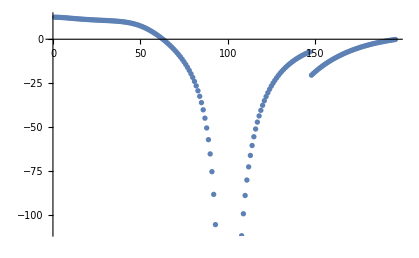

```mathematica
ListPlot[%341]
```

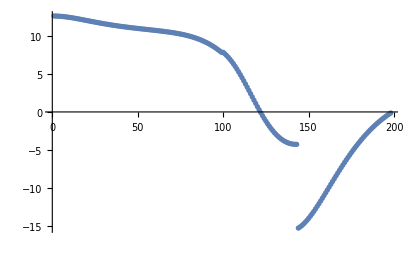

```mathematica
ListPlot[%326]
```

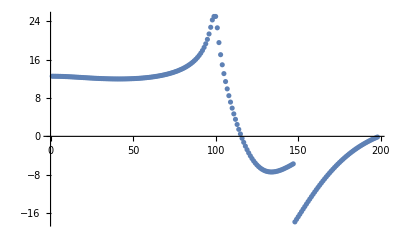

```mathematica
ListPlot[%320]
```

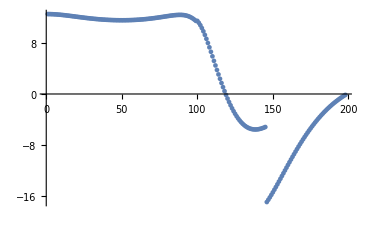

```mathematica
ListPlot[%313]
```

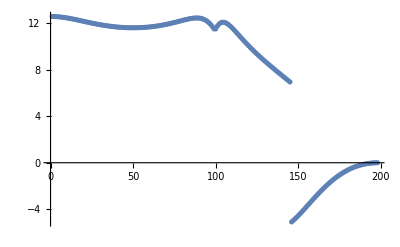

```mathematica
ListPlot[%305]
```

```mathematica
ListPlot[%284]
```

-Graphics-

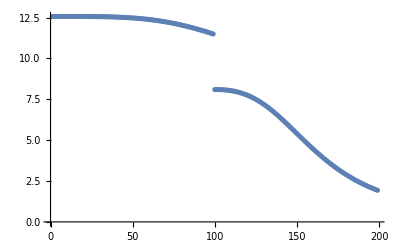

```mathematica
ListPlot[%278]
```

```mathematica
ListPlot[%272]
```

-Graphics-

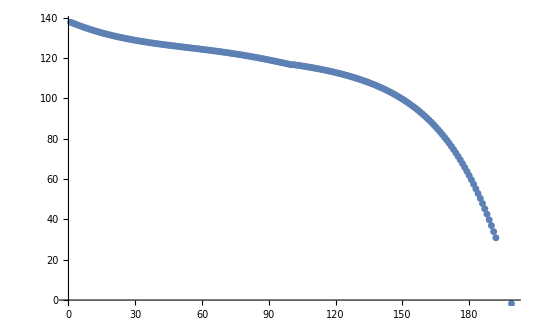

```mathematica
ListPlot[%244]
```

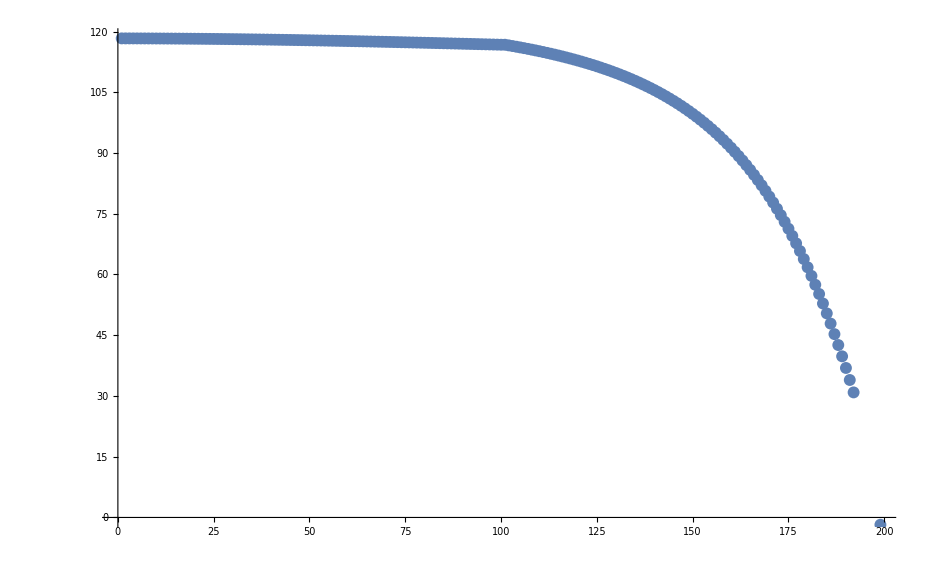

```mathematica
ListPlot[%237]
```

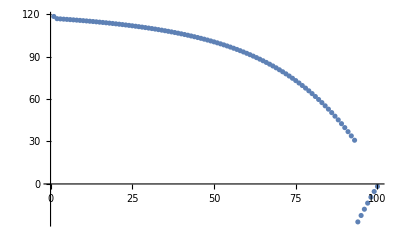

```mathematica
ListPlot[%227]
```

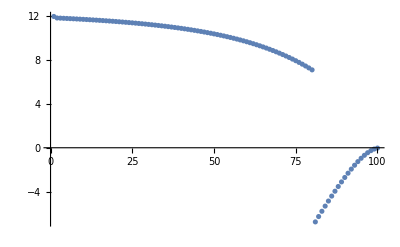

```mathematica
ListPlot[%221]
```

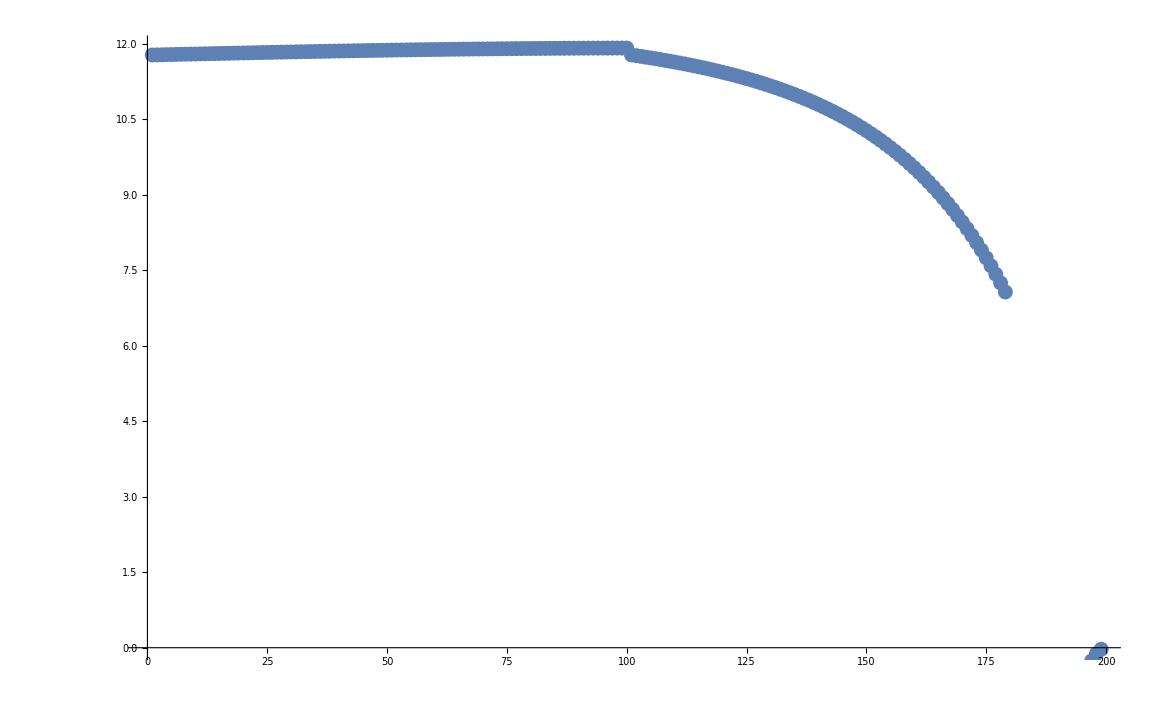

```mathematica
ListPlot[%213]
```

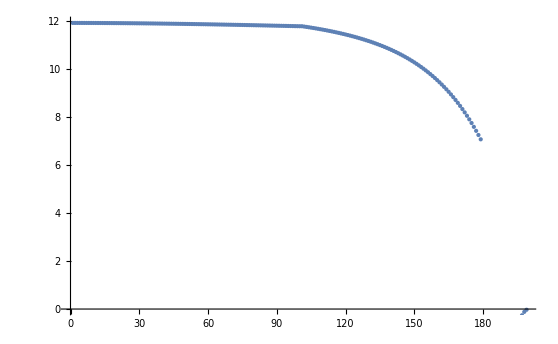

```mathematica
ListPlot[%174,PlotStyle->PointSize[Medium]]
```

```mathematica
Manipulate[Show[ParametricPlot[ReIm[(0.1(I - q - del*I))/2*( Exp[-I*ϕ])+ I (I - q - del*I)/2+(0.1(I - q - del*I))/2 ],{ϕ,0,π},PlotStyle->Orange]],{{q,Sqrt[-2]},Sqrt[-5],0},{del,0.0,1},{μ,0.00,1}]
```

```mathematica
((I - q - del*I)*0.1)/2*( Exp[-I*ϕ])+ I (I - q - del*I)/2+(0.1*(I - q - del*I))/2/.{ϕ->π,q->Sqrt[-2],del->0}
```

0.207107+0. ⅈ

```mathematica
FullSimplify[(1/2+ⅈ/2) (ⅈ-ⅈ √2)+1/2 (-ⅈ+ⅈ √2)]
```

```mathematica
-1/2+1/(√2)//N
```

0.207107

```mathematica
(I - Sqrt[-2])/2*I//N
```

0.207107+0. ⅈ

```mathematica
Integrate[2*x*-I/(2*(4*π)^(3/2))*Gamma[3/2]/((q0^2(x^2 + 2x - 1) - x*m^2)^(3/2)),{x,0,1}]
```

ConditionalExpression[(ⅈ (4 √(-q0^2)+(2 m^2)/(√(-m^2+2 q0^2))))/(16 π (m^4-4 m^2 q0^2+8 q0^4)), ]

```mathematica
(ⅈ (4 √(-q0^2)+(2 m^2)/(√(-m^2+2 q0^2))))/(16 π (m^4-4 m^2 q0^2+8 q0^4))/.{m->1,q0^2->p,q0^4->p^2}
```

(ⅈ (4 √-p+2/(√(-1+2 p))))/(16 (1-4 p+8 p^2) π)

```mathematica
(ⅈ (4 √-p+2/(√(-1+2 p))))/(16 (1-4 p+8 p^2) π)/.{p->En}
```

(ⅈ (4 √-En+2/(√(-1+2 En))))/(16 (1-4 En+8 En^2) π)

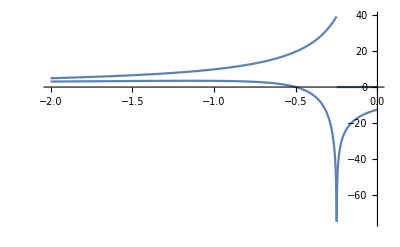

```mathematica
Plot[ReIm[1/(2*π^2)(ⅈ (4 √-En+2/(√(-1+2 En))))/(16 (1-4 En+8 En^2) π) + V0[Sqrt[En],Sqrt[En],1,1]],{En,-2,0},PlotRange->All]
```

```mathematica
Integrate[2*x*-I/(2*(4*π)^(3/2))*Gamma[3/2]/((q0^2(x(1-x)) - x*m^2)^(3/2)),{x,0,1}]
```

ConditionalExpression[-ⅈ/(8 π √(m^2/q0^2) √(q0^2/(m^2-q0^2)) (-m^2+q0^2)^(3/2)), ]

```mathematica
-ⅈ/(8 π √(m^2/q0^2) √(q0^2/(m^2-q0^2)) (-m^2+q0^2)^(3/2))/.{m->1}
```

```mathematica
FullSimplify[-ⅈ/(8 π √(1/q0^2) √(q0^2/(1-q0^2)) (-1+q0^2)^(3/2))]
```

```mathematica
(ⅈ √(1/q0^2) √(-q0^2/(-1+q0^2)))/(8 π √(-1+q0^2))/.{m->1,q0^2->p,q0^4->p^2}
```

```mathematica
(ⅈ √(-p/(-1+p)) √(1/q0^2))/(8 √(-1+p) π)/.{q0^2->p}
```

(ⅈ √(-p/(-1+p)) √(1/q0^2))/(8 √(-1+p) π)

```mathematica
-ⅈ/(8 (-1+p)^(3/2) √(p/(1-p)) π √(1/q0^2))
```

-ⅈ/(8 (-1+p)^(3/2) √(p/(1-p)) π √(1/q0^2))

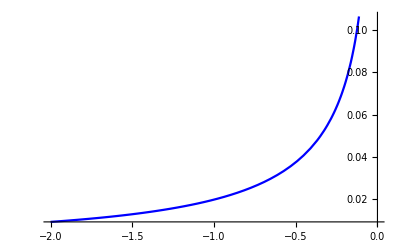

```mathematica
Plot[Im[(ⅈ √(-p/(-1+p)) √(1/p^2))/(8 √(-1+p) π)],{p,0,-2},PlotStyle->{Orange,Blue}]
```